Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{i→1.25 (655.-1. √(429025.-4. P))},{i→1.25 (655.+√(429025.-4. P))}}

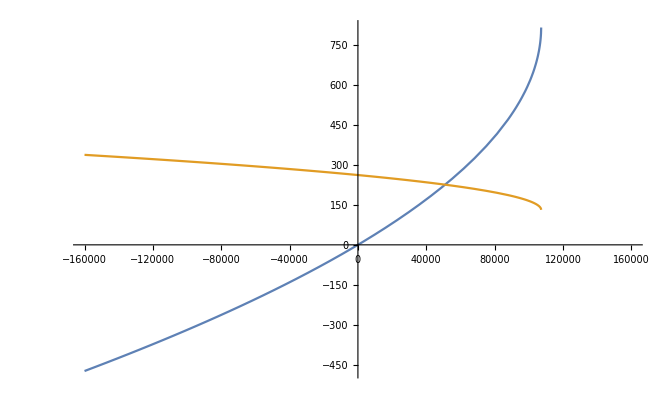

```mathematica
(*Clear[Voc,R,P]*)
Voc = 262;
R = .16;
(*P = 80000;*)
Clear[P];
Solve[i==P/(Voc-i*R),i]
Plot[{1.25 (655.-1. √(429025.-4. P)),Voc-R*(1.25 (655.-1. √(429025.-4. P)))},{P,-160000,160000}]
```

```mathematica
Voc-R*406
```

197.04

```mathematica
197*406
```

79982